```mathematica
SetDirectory@NotebookDirectory[]
```

/Users/leima/github/neuphysics/codebase/mma/dispersion-relation

```mathematica
Get["../../neupackage/mma/dispersion-relation.wl"]
```

```mathematica
pltcolors=ColorData[97,"ColorList"]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
pltmarkers={-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
(*SH[l_,m_]:=SphericalHarmonicY[l,m,theta,phi]*)
(*vvSHMatrix[theta,phi]-vvMatrix[theta,phi]//FullSimplify*)
```

## Spherical Harmonics

```mathematica
v[theta,phi]
```

{1,Cos[phi] Sin[theta],Sin[phi] Sin[theta],Cos[theta]}

```mathematica
vvMatrix[theta,phi]//MatrixForm
```

(1 | Cos[phi] Sin[theta] | Sin[phi] Sin[theta] | Cos[theta]
Cos[phi] Sin[theta] | Cos[phi]^2 Sin[theta]^2 | Cos[phi] Sin[phi] Sin[theta]^2 | Cos[phi] Cos[theta] Sin[theta]
Sin[phi] Sin[theta] | Cos[phi] Sin[phi] Sin[theta]^2 | Sin[phi]^2 Sin[theta]^2 | Cos[theta] Sin[phi] Sin[theta]
Cos[theta] | Cos[phi] Cos[theta] Sin[theta] | Cos[theta] Sin[phi] Sin[theta] | Cos[theta]^2)

```mathematica
Grid[
Table[
Table[SphericalHarmonicY[l,m,theta,phi]
,{m,-l,l,1}]
,{l,{0,1}}],
Frame->All]
```

1/(2 √π) |  | 
1/2 ⅇ^(-ⅈ phi) √(3/(2 π)) Sin[theta] | 1/2 √(3/π) Cos[theta] | -1/2 ⅇ^(ⅈ phi) √(3/(2 π)) Sin[theta]

```mathematica
vSH[theta,phi]
```

{2 √π SH[0,0,theta,phi],√((2 π)/3) (SH[1,-1,theta,phi]-SH[1,1,theta,phi]),ⅈ √((2 π)/3) (SH[1,-1,theta,phi]+SH[1,1,theta,phi]),2 √(π/3) SH[1,0,theta,phi]}

```mathematica
vvSHMatrix[theta,phi]//FullSimplify//MatrixForm
```

(4 π SH[0,0,theta,phi]^2 | 2 √(2/3) π SH[0,0,theta,phi] (SH[1,-1,theta,phi]-SH[1,1,theta,phi]) | 2 ⅈ √(2/3) π SH[0,0,theta,phi] (SH[1,-1,theta,phi]+SH[1,1,theta,phi]) | (4 π SH[0,0,theta,phi] SH[1,0,theta,phi])/(√3)
2 √(2/3) π SH[0,0,theta,phi] (SH[1,-1,theta,phi]-SH[1,1,theta,phi]) | 2/3 π (SH[1,-1,theta,phi]-SH[1,1,theta,phi])^2 | 2/3 ⅈ π (SH[1,-1,theta,phi]^2-SH[1,1,theta,phi]^2) | 2/3 √2 π SH[1,0,theta,phi] (SH[1,-1,theta,phi]-SH[1,1,theta,phi])
2 ⅈ √(2/3) π SH[0,0,theta,phi] (SH[1,-1,theta,phi]+SH[1,1,theta,phi]) | 2/3 ⅈ π (SH[1,-1,theta,phi]^2-SH[1,1,theta,phi]^2) | -2/3 π (SH[1,-1,theta,phi]+SH[1,1,theta,phi])^2 | 2/3 ⅈ √2 π SH[1,0,theta,phi] (SH[1,-1,theta,phi]+SH[1,1,theta,phi])
(4 π SH[0,0,theta,phi] SH[1,0,theta,phi])/(√3) | 2/3 √2 π SH[1,0,theta,phi] (SH[1,-1,theta,phi]-SH[1,1,theta,phi]) | 2/3 ⅈ √2 π SH[1,0,theta,phi] (SH[1,-1,theta,phi]+SH[1,1,theta,phi]) | 4/3 π SH[1,0,theta,phi]^2)

Imposing Axial symmetry,

```mathematica
nMatrixPhi[theta_]:=Integrate[vvMatrix[theta,phi]/(1-n Cos[theta]),
{phi,0,2Pi}]
```

```mathematica
nMatrixPhi[theta]//MatrixForm
```

((2 π)/(1-n Cos[theta]) | 0 | 0 | (2 π Cos[theta])/(1-n Cos[theta])
0 | (π Sin[theta]^2)/(1-n Cos[theta]) | 0 | 0
0 | 0 | (π Sin[theta]^2)/(1-n Cos[theta]) | 0
(2 π Cos[theta])/(1-n Cos[theta]) | 0 | 0 | (2 π Cos[theta]^2)/(1-n Cos[theta]))

```mathematica
Assuming[n∈Reals&&-1<n<1&&x∈Reals&&thetaInit>thetaEnd,
Integrate[
{
1/(1-n x),
x/(1-n x),
(x^2)/(1-n x),
(x^m)/(1-n x)
},{x,thetaInit,thetaEnd}]
]
```

$Aborted

```mathematica
intFun1[n_,thetaInit_,thetaEnd_]:=(-Log[1-n thetaEnd]+Log[1-n thetaInit])/n;
intFun2[n_,thetaInit_,thetaEnd_]:=(n (-thetaEnd+thetaInit)+Log[(-1+n thetaInit)/(-1+n thetaEnd)])/n^2;
intFun3[n_,thetaInit_,thetaEnd_]:=1/(2 n^3)(-n (thetaEnd-thetaInit) (2+n (thetaEnd+thetaInit))+2 Log[(-1+n thetaInit)/(-1+n thetaEnd)]);
intFunm[m_,n_,thetaInit_,thetaEnd_]:=1/(m n)(-1/n)^-m (-n)^-m (-thetaEnd^m Hypergeometric2F1[1,-m,1-m,1/(n thetaEnd)]+thetaInit^m Hypergeometric2F1[1,-m,1-m,1/(n thetaInit)]);
```

```mathematica
nMatrix[thetaInit_,thetaEnd_]:={
{2Pi intFun1[n,thetaInit,thetaEnd],0,0,2Pi intFun2[n,thetaInit,thetaEnd]},
{0,Pi (intFun1[n,thetaInit,thetaEnd]-intFun3[n,thetaInit,thetaEnd]),0,0},
{0,0,Pi (intFun1[n,thetaInit,thetaEnd]-intFun3[n,thetaInit,thetaEnd]),0},
{2Pi intFun2[n,thetaInit,thetaEnd],0,0,2Pi (intFun1[n,thetaInit,thetaEnd]-intFun3[n,thetaInit,thetaEnd])}
}
```

```mathematica
axialNMatrix[n_]=-nMatrix[ArcCos@0.9,(ArcCos[0.3]+ArcCos[0.9])/2]/((ArcCos[0.3]+ArcCos[0.9])/2)/(2Pi)+nMatrix[(ArcCos[0.3]+ArcCos[0.9])/2,ArcCos@0.3]/((ArcCos[0.3]+ArcCos[0.9])/2)/(2Pi)//FullSimplify;
axialNMatrix[n]//MatrixForm
```

((-1.16473 Log[1.-1.2661 n]+2.32947 Log[1.-0.858565 n]-1.16473 Log[1.-0.451027 n])/n | 0. | 0. | (0.297355+1.16473 Log[1.+0.374909/(0.789825-1. n)]-1.16473 Log[1.+1.05243/(1.16473-1. n)])/n^2
0. | (-0.582367 Log[0.678116+0.254232/(0.789825-1. n)]+0.582367 Log[0.525326+0.552869/(1.16473-1. n)]+n^2 (0.245402-0.582367 Log[0.789825-1. n]+1.16473 Log[1.16473-1. n]-0.582367 Log[2.21716-1. n]))/n^3 | 0. | 0.
0. | 0. | (-0.582367 Log[0.678116+0.254232/(0.789825-1. n)]+0.582367 Log[0.525326+0.552869/(1.16473-1. n)]+n^2 (0.245402-0.582367 Log[0.789825-1. n]+1.16473 Log[1.16473-1. n]-0.582367 Log[2.21716-1. n]))/n^3 | 0.
(0.297355+1.16473 Log[1.+0.374909/(0.789825-1. n)]-1.16473 Log[1.+1.05243/(1.16473-1. n)])/n^2 | 0. | 0. | (-1.16473 Log[0.678116+0.254232/(0.789825-1. n)]+1.16473 Log[0.525326+0.552869/(1.16473-1. n)]+n^2 (0.490803-1.16473 Log[0.789825-1. n]+2.32947 Log[1.16473-1. n]-1.16473 Log[2.21716-1. n]))/n^3)

```mathematica
axialNMatrixPrime[n_]={-axialNMatrix[n][[1]],axialNMatrix[n][[2]],axialNMatrix[n][[3]],axialNMatrix[n][[4]]};
```

```mathematica
axialEigenValues[n_]=Eigenvalues[axialNMatrixPrime[n]];
```

```mathematica
pltDataAxialEigenVlaues=Table[
{n,#}&/@axialEigenValues[n],
{n,-1,1,0.009}]//Transpose;
```

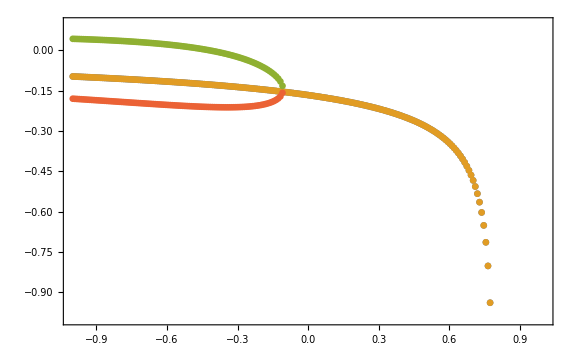

```mathematica
ListPlot[pltDataAxialEigenVlaues,Frame->True,PlotRange->{{-1,1},{-1,0.1}},ImageSize->Large]
```

## Analytical

```mathematica
Inverse[{{2Pi I1,0},{0,Pi(I1-I3)}}]//Simplify
```

{{1/(2 I1 π),0},{0,1/(I1 π-I3 π)}}

```mathematica
Integrate[Cos[x]^2,{x,0,2Pi}]
Integrate[Sin[x]^2,{x,0,2Pi}]
```

π

π

```mathematica
testMat=1/4{
{2I0,0,0,-2I1},
{0,-(I1-I2),0,0},
{0,0,-(I1-I2),0},
{2I1,0,0,-2I2}
};
%//MatrixForm
Eigenvalues@testMat//FullSimplify
```

(I0/2 | 0 | 0 | -I1/2
0 | 1/4 (-I1+I2) | 0 | 0
0 | 0 | 1/4 (-I1+I2) | 0
I1/2 | 0 | 0 | -I2/2)

{1/4 (-I1+I2),1/4 (-I1+I2),1/4 (I0-I2-√((I0-2 I1+I2) (I0+2 I1+I2))),1/4 (I0-I2+√((I0-2 I1+I2) (I0+2 I1+I2)))}

```mathematica
rotMat={
{1,0,0,0},
{0,0,0,1},
{0,1,0,0},
{0,0,1,0}
};
%//MatrixForm
rotMat.{a0,a1,a2,a3}
```

(1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 1 | 0 | 0
0 | 0 | 1 | 0)

{a0,a3,a1,a2}

```mathematica
testMatBD=rotMat.testMat.Inverse[rotMat];
%//MatrixForm
```

(I0/2 | -I1/2 | 0 | 0
I1/2 | -I2/2 | 0 | 0
0 | 0 | 1/4 (-I1+I2) | 0
0 | 0 | 0 | 1/4 (-I1+I2))

```mathematica
testMatBD//Eigensystem//MatrixForm
```

(1/4 (-I1+I2) | 1/4 (-I1+I2) | 1/4 (I0-I2-√(I0^2-4 I1^2+2 I0 I2+I2^2)) | 1/4 (I0-I2+√(I0^2-4 I1^2+2 I0 I2+I2^2))
{0,0,0,1} | {0,0,1,0} | {-(-I0-I2+√(I0^2-4 I1^2+2 I0 I2+I2^2))/(2 I1),1,0,0} | {-(-I0-I2-√(I0^2-4 I1^2+2 I0 I2+I2^2))/(2 I1),1,0,0})